VWAP market=96.7057

{{1329853410996,VwapAgent5,5,BUY,NoiseTraderAgent2,3,SELL,1600,99.},{1329853442432,NoiseTraderAgent4,636,SELL,VwapAgent5,599,BUY,553,98.},{1329853442746,NoiseTraderAgent4,642,SELL,VwapAgent5,599,BUY,1047,98.},{1329853471821,NoiseTraderAgent2,1227,SELL,VwapAgent5,1209,BUY,323,98.},{1329853471854,NoiseTraderAgent1,1231,SELL,VwapAgent5,1209,BUY,1277,98.},{1329853500774,NoiseTraderAgent2,1795,SELL,VwapAgent5,1794,BUY,986,97.},{1329853501327,NoiseTraderAgent2,1806,SELL,VwapAgent5,1794,BUY,614,97.},{1329853531265,NoiseTraderAgent1,2387,SELL,VwapAgent5,2379,BUY,1600,96.},{1329853560745,NoiseTraderAgent2,2981,SELL,VwapAgent5,2980,BUY,962,94.},{1329853560788,NoiseTraderAgent4,2983,SELL,VwapAgent5,2980,BUY,638,94.},{1329853593893,NoiseTraderAgent3,3619,SELL,VwapAgent5,3561,BUY,1116,95.},{1329853593943,NoiseTraderAgent2,3621,SELL,VwapAgent5,3561,BUY,484,95.},{1329853622383,NoiseTraderAgent2,4174,SELL,VwapAgent5,4137,BUY,1230,98.},{1329853623126,NoiseTraderAgent1,4186,SELL,VwapAgent5,4137,BUY,370,98.},{1329853653686,NoiseTraderAgent2,4808,SELL,VwapAgent5,4748,BUY,278,94.},{1329853664662,NoiseTraderAgent4,5039,SELL,VwapAgent5,4748,BUY,1322,94.},{1329853681636,NoiseTraderAgent4,5384,SELL,VwapAgent5,5363,BUY,1067,94.},{1329853681755,NoiseTraderAgent1,5388,SELL,VwapAgent5,5363,BUY,533,94.},{1329853711366,NoiseTraderAgent0,5974,SELL,VwapAgent5,5959,BUY,600,94.},{1329853711516,NoiseTraderAgent1,5978,SELL,VwapAgent5,5959,BUY,1000,94.}}

Set::write: Tag Times in executionPricesLine$8950\ Null is Protected.

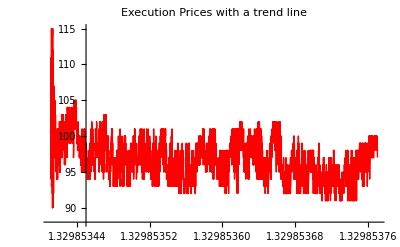

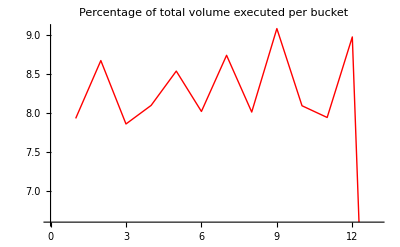

Testing for normal distribution of executed prices

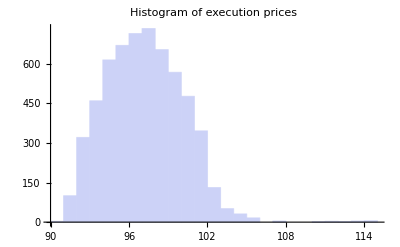

| Statistic | P-Value
Shapiro-Wilk | Indeterminate | Indeterminate

Indeterminate

| Statistic | P-Value
Anderson-Darling | 37.572 | 0.

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

Testing for normal distribution of submitted prices

-Graphics-

| Statistic | P-Value
Shapiro-Wilk | Indeterminate | Indeterminate

Indeterminate

| Statistic | P-Value
Anderson-Darling | 37.572 | 0.

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Anderson-Darling test.

Import::nffil: File not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, executionTimestamp$8950[#1] > start$8950 && newOrderPrice$8950[#1] > 0. &].

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Testing for normal distribution of new order prices

Histogram::ldata: Function[] is not a valid dataset or list of datasets.

Show::gtype: Histogram is not a type of graphics.

Show[Histogram[Function[]],PlotLabel→Histogram of new order prices]

ShapiroWilkTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

ShapiroWilkTest[Function[],HypothesisTestData][TestDataTable]

ShapiroWilkTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

ShapiroWilkTest[Function[],HypothesisTestData][TestConclusion]

AndersonDarlingTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

AndersonDarlingTest[Function[],Automatic,HypothesisTestData][TestDataTable]

AndersonDarlingTest::rectuv: The argument Function[] should be a vector or matrix of real numbers with positive variance.

General::stop: Further output of AndersonDarlingTest :: rectuv will be suppressed during this calculation.

AndersonDarlingTest[Function[],Automatic,HypothesisTestData][TestConclusion]

```mathematica
ClearAll[report];

report[path_String, filter_Integer, buckets_Integer, algoName_String]:=Module[{executionTimestamp, initiatingTrader, restingTrader,executionPrice, executionVolume, executionsData, start, stop,executions,executionPricesTimestamps, executionPrices,executionVolumesTimestamps, executionVolumes,executionVolumeTimesPrice,executionsAlgo,executionsAlgoVolumes,executionsAlgoVolumeTimesPrice,executionVolumesBucketed, executionAverageVolumesByBucket,executionPricesLine, newOrderTimestamp, newOrderPrice, newOrderVolume, newOrdersData,newOrders,newOrdersPrices},

executionTimestamp = #[[1]]&;
initiatingTrader=#[[2]]&;
restingTrader=#[[5]]&;
executionPrice = #[[9]]&;
executionVolume = #[[8]]&;

executionsData = Import[path<> "executions.log"];
start = Min[executionTimestamp[#]&/@executionsData] (*+  filter * 60 * 1000*);
stop = Max[executionTimestamp[#]&/@executionsData];
executions = Sort[Select[executionsData,(* executionTimestamp[#] > start*)initiatingTrader[#]≠algoName && restingTrader[#]≠algoName&], OrderedQ[{executionTimestamp[#],executionTimestamp[#2]}]&];
executionPricesTimestamps ={ executionTimestamp[#], executionPrice[#]}&/@executions;
executionPrices = executionPrice[#]&/@executions;
executionVolumesTimestamps={ executionTimestamp[#], executionVolume[#]}&/@executions;
executionVolumes = executionVolume[#]&/@executions;

executionVolumeTimesPrice = Total[ executionPrice[#] executionVolume[#]&/@executions];
Print["VWAP market="<>ToString[executionVolumeTimesPrice/Total[executionVolumes]]];

executionsAlgo = Sort[Select[executionsData,(* executionTimestamp[#] > start*)initiatingTrader[#]==algoName || restingTrader[#]==algoName&], OrderedQ[{executionTimestamp[#],executionTimestamp[#2]}]&];
executionsAlgoVolumes = executionVolume[#]&/@executionsAlgo;
executionsAlgoVolumeTimesPrice = Total[ executionPrice[#] executionVolume[#]&/@executionsAlgo];
Print["VWAP algo="<>ToString[executionsAlgoVolumeTimesPrice/Total[executionsAlgoVolumes]]];

executionPricesLine = Fit[executionPricesTimestamps, {1,x}, x];
Print[Show[ListLinePlot[executionPricesTimestamps, PlotStyle->Red], Plot[executionPricesLine, {x, start, stop}, PlotStyle->Green], PlotLabel->"Execution Prices with a trend line"]];

executionVolumesBucketed =Gather[executionVolumesTimestamps, Quotient[executionTimestamp[#]-start,(stop-start)/buckets]==Quotient[executionTimestamp[#2]-start,(stop-start)/buckets]&] ;
executionAverageVolumesByBucket = Total[Map[#[[2]]&,#]]/Total[executionVolumes]*100&/@executionVolumesBucketed;
Print[Show[ListLinePlot[executionAverageVolumesByBucket , PlotStyle->Red], PlotLabel->"Percentage of total volume executed per bucket"]];

Print["Testing for normal distribution of executed prices"];
Print[Show[Histogram[executionPrices], PlotLabel->"Histogram of execution prices"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];

Print["Testing for normal distribution of submitted prices"];
Print[Show[Histogram[executionPrices], PlotLabel->"Histogram of execution prices"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[executionPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[executionPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];

newOrderTimestamp = #[[1]]&;
newOrderPrice = #[[8]]&;
newOrderVolume = #[[7]]&;
newOrdersData = Import[path<> "newOrders.log"];
newOrders = Sort[Select[newOrdersData, executionTimestamp[#] > start && newOrderPrice[#]>0.&], OrderedQ[{newOrderTimestamp[#],newOrderTimestamp[#2]}]&];
newOrdersPrices = newOrderPrice[#]&/@newOrders;

Print["Testing for normal distribution of new order prices"];
Print[Show[Histogram[newOrdersPrices], PlotLabel->"Histogram of new order prices"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestDataTable"]];
Print[ShapiroWilkTest[newOrdersPrices,"HypothesisTestData"]["TestConclusion"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestDataTable"]];
Print[AndersonDarlingTest[newOrdersPrices,Automatic,"HypothesisTestData"]["TestConclusion"]];
];

report["/Users/jakubkozlowski/Programming/intellij/eugene/experiment/vwap-no-error/runner/", 2, 12, "VwapAgent5"]
```